## Constants

```mathematica
hbar=1.;
c=2.995*10^5(*km/s*);
```

## Yukawa potential:

```mathematica
Uattractive[r_]=+αχ/r ⅇ^(-mϕ r)
Urepulsive[r_]=-αχ/r ⅇ^(-mϕ r)
```

(ⅇ^(-mϕ r) αχ)/r

-(ⅇ^(-mϕ r) αχ)/r

## Phase shift δl in classical regime

### Exact integral for δl

Landau, Lifshitz, p. 487, (126.4) :

```mathematica
integrandδlclass[l_,U_,r_]=1/hbar √(2m(EE-U)-(hbar^2(l+1/2)^2)/r^2)
```

1.35286+1. √(-2.25/r^2+200. (5.57412×10^-8-U))

```mathematica
integrandδlclass2[l_,U_,r_]=k*c^2*(√(1-r0^2/r^2-U/(EE*c^2))-√(1-r0^2/r^2))
```

2.995×10^8 (-√(1-89700.3/r^2)+√(1-89700.3/r^2-0.0002 U))

```mathematica
(*δlclassattractive[l_]:=NIntegrate[integrandδlclass[l,Uattractive[r],r],{r,r0,∞}](*//.{r0-> l/k}*)
δlclassrepulsive[l_]:=NIntegrate[integrandδlclass[l,Uattractive[r],r],{r,r0,∞}](*//.{r0-> l/k}*)*)
```

### Derivation of the approximate integral for δl

Landau, Lifshitz, ‘The quasi-classical case’, p. 487, (126.4) :

```mathematica
integrandδlclass[U]=1/hbar √(2m(EE-U)-(hbar^2(l+1/2)^2)/r^2)-k+1/2 π (l+1/2)-k r0
```

2.32281-0.033389 r0+√(-9/(4 r^2)+2 m (EE-U))

```mathematica
Normal[Series[integrandδlclass[U],{U,0,1}]]
```

-k+(√(2 EE m-(hbar^2 (1/2+l)^2)/r^2))/hbar-(m U)/(hbar √(2 EE m-(hbar^2 (1/2+l)^2)/r^2))

```mathematica
integrandδlclassappr1[r]=Part[Normal[Series[integrandδlclass[U],{U,0,1}]],{1,2}]
```

-k+(√(2 EE m-(hbar^2 (1/2+l)^2)/r^2))/hbar

```mathematica
integrandδlclassappr1[r]//.{2m EE-> hbar^2 k^2}//.{(l+1/2)^2-> l^2}//.{l-> k*r0}//.{√(hbar^2 k^2-(hbar^2 k^2 r0^2)/r^2)-> hbar k √(1-r0^2/r^2)}
```

-k+k √(1-r0^2/r^2)

```mathematica
δlclassappr1[r]=Integrate[integrandδlclassappr1[r]//.{2m EE-> hbar^2 k^2}//.{(l+1/2)^2-> l^2}//.{l-> k*r0}//.{√(hbar^2 k^2-(hbar^2 k^2 r0^2)/r^2)-> hbar k √(1-r0^2/r^2)},{r,r0,∞},Assumptions-> {r0>0}](*Need all of these approximations.*)
```

k (r0-(π r0)/2)

```mathematica
δlclassappr2[r]=integrandδlclassappr2[r]=Part[Normal[Series[integrandδlclass[U],{U,0,1}]],3]
```

-(m U)/(hbar √(2 EE m-(hbar^2 (1/2+l)^2)/r^2))

```mathematica
δlclassappr=δlclassappr1[r]+δlclassappr2[r]+1/2 π(l+1/2)-k r0//.{2m EE-> hbar^2 k^2}//.{l+1/2-> l}//.{l-> k*r0}//.{(m U)/(hbar √(hbar^2 k^2-(hbar^2 k^2 r0^2)/r^2))-> (m U)/(hbar k √(1-r0^2/r^2))}//Expand
```

-(m U)/(hbar k √(1-r0^2/r^2))

Landau, Lifshitz, p. 473, (123.1) :

```mathematica
ntegrandδlclassappr[U_,r_]=-(mχ/2)/hbar^2*U*1/(√(k^2-(l+1/2)^2/r^2))
```

### Approximate integral for δl

Landau, Lifshitz, p. 473, (123.1) :

```mathematica
integrandδlclassappr[U_,r_]:=-m/hbar^2*U*1/(√(k^2-(l+1/2)^2/r^2))
```

### Analytical solution of the integral for δl

Phase shift δl:

```mathematica
integrandδlclassappr[Uattractive[r],r]//.{(l+1/2)^2-> l^2}//.{l-> k*r0,m-> mχ/2}
```

-(ⅇ^(-mϕ r) mχ αχ)/(2 hbar^2 r √(k^2-(k^2 r0^2)/r^2))

```mathematica
δlclassapprattractive[l_]=Integrate[integrandδlclassappr[Uattractive[r],r]//.{(l+1/2)^2-> l^2}//.{l-> k*r0,m-> mχ/2},{r,r0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0}]//.{r0-> l/k}
```

-(mχ αχ BesselK[0,(l mϕ)/k])/(2 hbar^2 k)

```mathematica
δlclassapprrepulsive[l_]=Integrate[integrandδlclassappr[Urepulsive[r],r]//.{(l+1/2)^2-> l^2}//.{l-> k*r0,m-> mχ/2},{r,r0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0}]//.{r0-> l/k}
```

(mχ αχ BesselK[0,(l mϕ)/k])/(2 hbar^2 k)

### Comparison of solutions for δl

```mathematica
m=mχ/2;
k=m v/c;
EE=(hbar^2 k^2)/(2 m);
hbar= 1.;
αχ= 10.^-2;
mχ= 200.;
 mϕ= 10.^-3;
l=1.;
r0=l/k
v= 10.;
```

299.5

```mathematica
δlclassapprattractive[l]
```

-411.51

```mathematica
δlclassattractive=NIntegrate[integrandδlclass[l,Uattractive[r],r],{r,r0,(*∞*)100000.},PrecisionGoal->20,MinRecursion-> 10,MaxRecursion-> 15]-k+1/2 π (l+1/2)-k r0 (*Doesn't work well. Numerically very unstable.*)
```

135201.+57.4594 ⅈ

```mathematica
δlclassattractive2=NIntegrate[integrandδlclass2[l,Uattractive[r],r],{r,r0,(*∞*)10^2 r0},PrecisionGoal->20,MinRecursion-> 10,MaxRecursion-> 15]
```

-411.51+0.0104102 ⅈ

## Transfer cross section σT

Sean’s formula, PRD87.115007, p.6, eqn. (9):

```mathematica
integrandσT[l_]=(l+1)*Sin[δl[l+1]-δl[l]]^2(*(δl[l+1]-δl[l])^2*)//FullSimplify//Expand
```

Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2+l Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(2 hbar^2 k)]^2

```mathematica
σT=(4π)/k^2*Integrate[integrandσT[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}] (*Integration with lmin as lower limit doesn't work.*)
```

1/k^2 4 π Integrate[1/(hbar^4 k^2)(1+l) (mχ αχ BesselK[0,(l mϕ)/k]-mχ αχ BesselK[0,((1+l) mϕ)/k])^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]

```mathematica
integrandσTappr[l_]=(l+1)*Sin[δlappr[l+1]-δlappr[l]]^2(*(δl[l+1]-δl[l])^2*)//FullSimplify//Expand
```

Sin[(ⅇ^(-((1+l) mϕ)/k) (-√l+ⅇ^(mϕ/k) √(1+l)) mχ √(π/2) αχ)/(2 hbar^2 √k √l √(1+l) √mϕ)]^2+l Sin[(ⅇ^(-((1+l) mϕ)/k) (-√l+ⅇ^(mϕ/k) √(1+l)) mχ √(π/2) αχ)/(2 hbar^2 √k √l √(1+l) √mϕ)]^2

```mathematica
σTappr=(4π)/k^2*Integrate[integrandσTappr[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

$Aborted

```mathematica
integrandσTN[l_]=(l+1)*Sin[δl[l+1]-δl[l]]^2(*(δl[l+1]-δl[l])^2*)//.{k->mχ v/2,mχ-> 200, mϕ-> 0.00003,v-> 10/(2.99*10^5),αχ-> 1.6*10^-6,hbar-> 1}
```

(1+l) Sin[0.04784 BesselK[0,0.00897 l]-0.04784 BesselK[0,0.00897 (1+l)]]^2

```mathematica
σT=(4π)/k^2*NIntegrate[integrandσTN[l],{l,(*lmin*)0,(*∞*)10^5}]//.{k->mχ v/2,mχ-> 200, mϕ-> 0.00003,v-> 10/(2.99*10^5),αχ-> 1.6*10^-6,hbar-> 1}
```

19137.3

```mathematica
21419/19137.27625830608
```

1.11923

```mathematica
integrandσTN[l_]=(l+1)*Sin[δl[l+1]-δl[l]]^2(*(δl[l+1]-δl[l])^2*)//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}
```

(1+l) Sin[2.99 BesselK[0,0.00598 l]-2.99 BesselK[0,0.00598 (1+l)]]^2

```mathematica
σT=(4π)/k^2*NIntegrate[integrandσTN[l],{l,(*lmin*)0,(*∞*)(*10^5*)500}]//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}
```

16509.7

```mathematica
16519.358425530132/15429
```

1.07067

```mathematica
16519.358425530132/16333
```

1.01141

```mathematica
σTplot[lmax_]:=(4π)/k^2*NIntegrate[integrandσTN[l],{l,(*lmin*)0,(*∞*)(*10^5*)lmax}]//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}
```

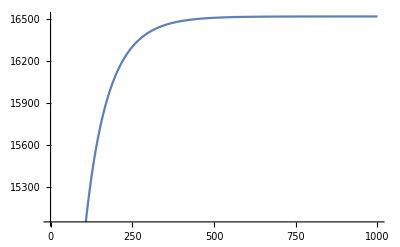

```mathematica
Plot[σTplot[lmax],{lmax,0,1000}]
```

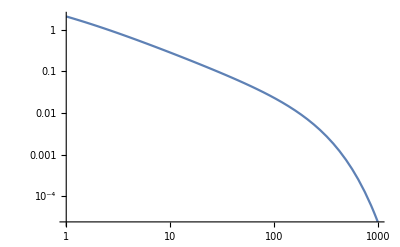

```mathematica
LogLogPlot[Abs[δl[l+1]-δl[l]//.{k->mχ v/2,mχ-> 1000, mϕ-> 0.001,v-> 100/(2.99*10^5),αχ-> 0.001,hbar-> 1}],{l,1,1000}]
```

```mathematica
integrandσT1[l_]=l*Sin[δl[l+1]-δl[l]]^2//.{(mχ αχ)/(hbar^2 k)-> c}
integrandσT2[l_]=Sin[δl[l+1]-δl[l]]^2//.{(mχ αχ)/(hbar^2 k)-> c}
```

l Sin[c BesselK[0,(l mϕ)/k]-c BesselK[0,((1+l) mϕ)/k]]^2

Sin[c BesselK[0,(l mϕ)/k]-c BesselK[0,((1+l) mϕ)/k]]^2

```mathematica
Integrate[integrandσT[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]
```

Integrate[(1+l) Sin[(mχ αχ (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k]))/(hbar^2 k)]^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]

Formula Buckley, Fox, 0911.3898, p.2, eqn. (7):

```mathematica
integrandσT1Buckley[l_]=(2l+1)*Sin[δl[l]]^2//.{(mχ αχ)/(hbar^2 k)-> c}//FullSimplify
integrandσT2Buckley[l_]=-(2l+1)*Sin[δl[l]]*Sin[δl[l+1]]*Cos[δl[l+1]-δl[l]]//.{(mχ αχ)/(hbar^2 k)-> c}//FullSimplify
```

(1+2 l) Sin[c BesselK[0,(l mϕ)/k]]^2

-(1+2 l) Cos[c (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k])] Sin[c BesselK[0,(l mϕ)/k]] Sin[c BesselK[0,((1+l) mϕ)/k]]

```mathematica
Integrate[integrandσT1Buckley[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]
```

Integrate[(1+2 l) Sin[c BesselK[0,(l mϕ)/k]]^2,{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0,c>0}]

```mathematica
Integrate[integrandσT2Buckley[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

Integrate[-(1+2 l) Cos[c (BesselK[0,(l mϕ)/k]-BesselK[0,((1+l) mϕ)/k])] Sin[c BesselK[0,(l mϕ)/k]] Sin[c BesselK[0,((1+l) mϕ)/k]],{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]

## Differential cross section dσ/dΩ

See Buckley, Fox, 0911.3898, p.2, eqn. (5):

```mathematica
integranddσdΩ[l_]=(2l+1)*ⅇ^(ⅈ*δl[l])*LegendreP[l,Cos[θ]]* Sin[δl[l]]//FullSimplify
```

-1/2 ⅈ (-1+ⅇ^((2 ⅈ mχ αχ BesselK[0,(l mϕ)/k])/(hbar^2 k))) (1+2 l) LegendreP[l,Cos[θ]]

```mathematica
Integrate[integranddσdΩ[l],{l,(*lmin*)0,∞},Assumptions-> {αχ >0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]
```

Integrate[-1/2 ⅈ (-1+ⅇ^((2 ⅈ mχ αχ BesselK[0,(l mϕ)/k])/(hbar^2 k))) (1+2 l) LegendreP[l,Cos[θ]],{l,0,∞},Assumptions→{αχ>0,mϕ>0,mχ>0,hbar>0,k>0,r0>0,l>0}]